## Numerical Example (Homog. b.c. for u and p):

```mathematica
lambda=1;
mu=1;
alpha=1;
c0=1e-05;
K=perm*IdentityMatrix[2];
perm=1,1e-03,...,1e-12;
```

```mathematica
Clear[lambda,mu,alpha,c0]
```

### Displacement :

```mathematica
u[x_,y_,t_]:={x(1-x)y(1-y),x(1-x)y(1-y)}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{0,0}

```mathematica
u[1,y,t]
```

{0,0}

```mathematica
u[x,0,t]
```

{0,0}

```mathematica
u[x,1,t]
```

{0,0}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

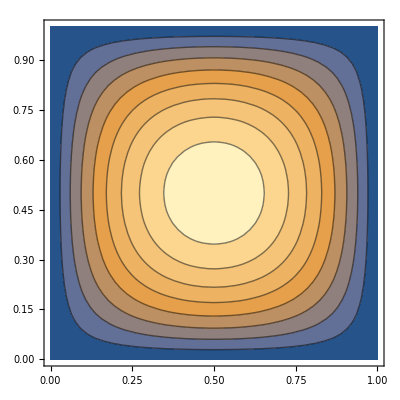

```mathematica
ContourPlot[Sqrt[(x(1-x)y(1-y))^2+(x(1-x)y(1-y))^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:= x(1-x)y(1-y)
```

```mathematica
p[0,y,t]
```

0

```mathematica
p[1,y,t]
```

0

```mathematica
p[x,0,t]
```

0

```mathematica
p[x,1,t]
```

0

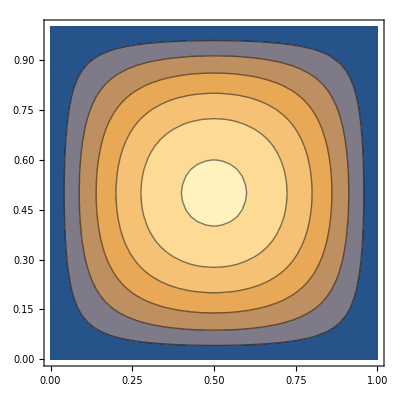

```mathematica
ContourPlot[p[x,y,t],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
Gradu[x_,y_,t_]:={{D[u[x,y,t][[1]], x],D[u[x,y,t][[1]], y]},{D[u[x,y,t][[2]], x],D[u[x,y,t][[2]], y]}}
```

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{(-1+2 x) (-1+y) y,1/2 (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2))},{1/2 (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2)),(-1+x) x (-1+2 y)}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
Sigmae[x_,y_,t_]:=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

```mathematica
Sigmae[x,y,t]
```

{{lambda (-1+2 x) (-1+y) y+2 mu (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y),mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2))},{mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2)),lambda (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y)+2 mu (-1+x) x (-1+2 y)}}

Let us define the stress function as the previous expression :

### Stress:

```mathematica
Sigma[x_,y_,t_]:=Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

```mathematica
Sigma[x,y,t]
```

{{-alpha (-1+x) x (-1+y) y+lambda (-1+2 x) (-1+y) y+2 mu (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y),mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2))},{mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2)),-alpha (-1+x) x (-1+y) y+lambda (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y)+2 mu (-1+x) x (-1+2 y)}}

ContourPlot of the Magnitude of the first row of σ :

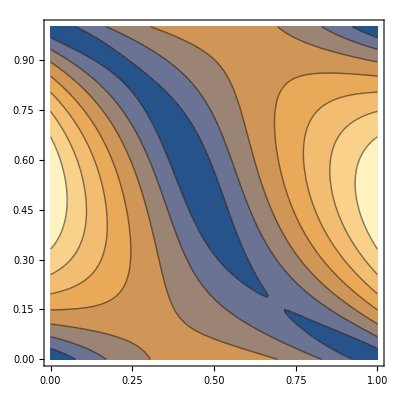

```mathematica
ContourPlot[Sqrt[(-alpha (-1+x) x (-1+y) y+lambda (-1+2 x) (-1+y) y+2 mu (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y))^2+(mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2)))^2]/.{lambda->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

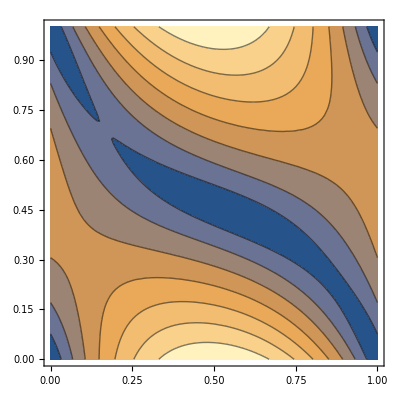

```mathematica
ContourPlot[Sqrt[(mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2)))^2+(-alpha (-1+x) x (-1+y) y+lambda (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y)+2 mu (-1+x) x (-1+2 y))^2]/.{lambda->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,1/2 (x+(-1+y) y-2 x y^2+x^2 (-1+2 y))},{1/2 (-x+x^2+y-2 x^2 y-y^2+2 x y^2),0}}

ContourPlot of the element in the first row and second column of the rotation:

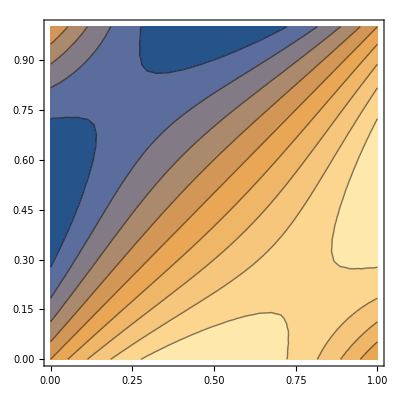

```mathematica
ContourPlot[1/2 (x+(-1+y) y-2 x y^2+x^2 (-1+2 y)),{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
K = perm*IdentityMatrix[2];
```

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{-perm (-1+2 x) (-1+y) y,-perm (-1+x) x (-1+2 y)}

```mathematica
z[x_,y_,t_]:={-perm (-1+2 x) (-1+y) y,-perm (-1+x) x (-1+2 y)}
```

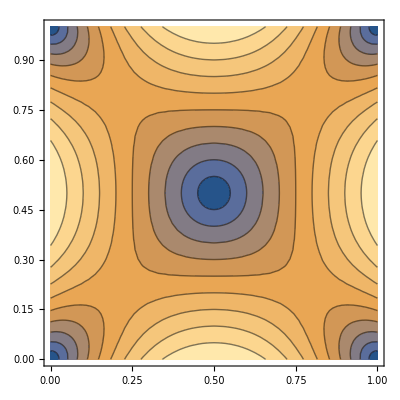

```mathematica
ContourPlot[Sqrt[(-perm (-1+2 x) (-1+y) y)^2+(-perm (-1+x) x (-1+2 y))^2]/.perm->1,{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{-alpha (-1+x) x (-1+y) y+lambda (-1+2 x) (-1+y) y+2 mu (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y),mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2))},{mu (-((-1+y) y)+x^2 (-1+2 y)+x (1-4 y+2 y^2)),-alpha (-1+x) x (-1+y) y+lambda (-1+2 x) (-1+y) y+lambda (-1+x) x (-1+2 y)+2 mu (-1+x) x (-1+2 y)}}

```mathematica
f[x_,y_,t_]:={-Div[{Sigma[x,y,t][[1,1]],Sigma[x,y,t][[1,2]]},{x,y}],-Div[{Sigma[x,y,t][[2,1]],Sigma[x,y,t][[2,2]]},{x,y}]}
```

```mathematica
f[x,y,t]//Simplify
```

{alpha (-1+2 x) (-1+y) y+lambda (-1+x (2-4 y)+4 y-2 y^2)-mu (1+2 x^2+4 x (-1+y)-6 y+4 y^2),alpha (-1+x) x (-1+2 y)+lambda (-1-2 x^2-4 x (-1+y)+2 y)-mu (1-6 x+4 x^2-4 y+4 x y+2 y^2)}

### Source term q :

```mathematica
u[x,y,t]
```

{(1-x) x (1-y) y,(1-x) x (1-y) y}

```mathematica
z[x,y,t]
```

{-perm (-1+2 x) (-1+y) y,-perm (-1+x) x (-1+2 y)}

```mathematica
D[c0 p[x,y,t]+alpha (D[u[x,y,t][[1]],x]+D[u[x,y,t][[2]],y]),t]+D[z[x,y,t][[1]],x]+D[z[x,y,t][[2]],y]//Simplify
```

-2 perm (-x+x^2+(-1+y) y)

```mathematica
q[x_,y_,t_]:=-2 perm (-x+x^2+(-1+y) y)
```

When t0=0 (stationary system)

```mathematica
D[z[x,y,t][[1]],x]+D[z[x,y,t][[2]],y]//Simplify
```

-2 perm (-x+x^2+(-1+y) y)